```mathematica
<<"/Users/rusi/Google Drive/topological-phases_1/MathematicaFolder/MarkovianNetworkPackage2.m"
<<"/Users/rusi/Google Drive/topological-phases_1/MathematicaFolder/SSHLibraryPackageSept2016.m"
```

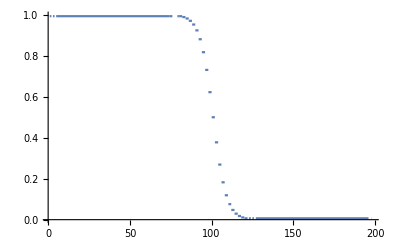

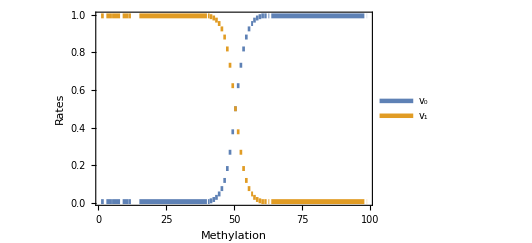

```mathematica
Ntval=100;s2val=1.0;Plot[{1/(1+Exp[-EtIn1[i,Ntval,1,s2val,1]])},{i,1,2*Ntval},PlotRange->All]
Plot[{1/(1+Exp[+EtIn1[2*i,Ntval,1,s2val,1]]),1/(1+Exp[-EtIn1[2 i,Ntval,1,s2val,1]])},{i,1,Ntval},PlotRange->All,PlotStyle->{Thickness[0.009]}, Frame->True,FrameLabel->{"Methylation", "Rates"},LabelStyle->{32,Black},PlotLegends->Placed[LineLegend[{"v_0","v_1"},LabelStyle->{GrayLevel[0.3],Bold,32},LegendLayout->{"Row",2}],{0.77,0.57}],AxesOrigin->{-0.0,0}]
```

```mathematica
s1val = 10.0;
λ1=λup[1.5,1,1.5,1,s1val/(1+Exp[-EtIn1[20,Ntval,1,s2val,1.0]]),s1val/(1+Exp[EtIn1[20,Ntval,1,s2val,1.0]])]
λ2=λdown[1.5,1,1.5,1,s1val/(1+Exp[-EtIn1[20,Ntval,1,s2val,1.0]]),s1val/(1+Exp[EtIn1[20,Ntval,1,s2val,1.0]])]
Tab1={{λ1,-0.02},{λ1,0.30}}
Tab2={{λ2,-0.02},{λ2,0.30}}
```

0.4

-0.400001

{{0.4,-0.02},{0.4,0.3}}

{{-0.400001,-0.02},{-0.400001,0.3}}

```mathematica
Ntval=200;h1val = 1.0; h2val = 1.0;h3val=1.0;h4val=1.0;Elval=0.0;Eaval=1.0;
s1val = 10.0;s2val =1.0;t1val = 1Exp[-1/4];t2val = 1.5Exp[1/4]; b1val = 1.5Exp[1/4];b2val = 1.0Exp[-1/4];
Wopt=WRectangleAllLinksSqJControl[s1val, s2val, t1val,t2val, b1val, b2val, h1val, h2val,h3val,h4val,Eaval,Elval,Ntval];
startvec=Re[Eigenvectors[Re[Wopt],1,Method->{"Arnoldi",BasisSize->Ntval,MaxIterations->100000,"Criteria"->"RealPart"}][[1]]];
AbsoluteTiming[Eigs22001=Table[{λ,Re[Eigenvalues[SparseArray[Re[WRectangleAllLinksSqJOptimized[s1val, s2val, t1val,t2val, b1val, b2val, h1val, h2val,h3val,h4val,Eaval,Elval,Ntval,   λ,Wopt]]],3,Method->{"Arnoldi",BasisSize->2Ntval,MaxIterations->100000,"Criteria"->"RealPart"}][[1]]]},
{λ,-0.4875,0.4875,0.025}];]
AbsoluteTiming[Eigs22002=Table[{λ,Re[Eigenvalues[Re[WRectangleAllLinksSqJOptimized[s1val, s2val, t1val,t2val, b1val, b2val, h1val, h2val,h3val,h4val,Eaval,Elval,Ntval,    λ,Wopt]],1,Method->{"Arnoldi",BasisSize->2Ntval,MaxIterations->100000,"Criteria"->"RealPart","StartingVector"->startvec}][[1]]]},
{λ,-0.4875,0.4875,0.025}];]
```

{36.84595,Null}

{37.35497,Null}

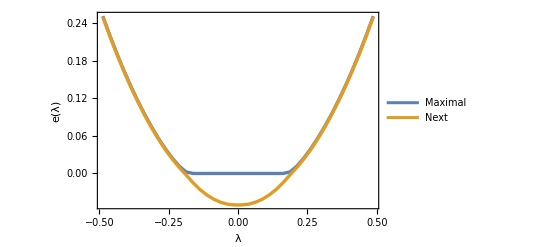

```mathematica
ListPlot[{Eigs22002,Eigs22001},PlotRange->All,Joined->True,PlotStyle->{Thickness[0.006]},PlotLegends->{"Maximal","Next ","N=200 2 ","N=150 2"}, Frame->True,FrameLabel->{"λ", "e(λ)"},LabelStyle->{22,Black}]
```

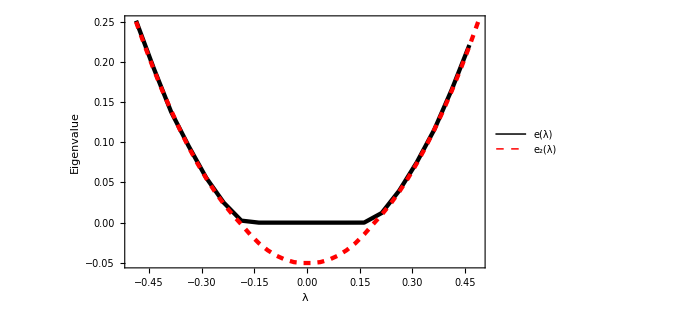

```mathematica
ListPlot[{Eigs22002,Eigs22001},PlotRange->All,Joined->True,PlotStyle->{{Thickness[0.006],Black},{Thickness[0.006],Red,Dashed}}, Frame->True,FrameLabel->{"λ", "Eigenvalue"},LabelStyle->{22,Black},PlotLegends->Placed[LineLegend[{"e(λ)","e_2(λ)","N=1600","N=3200"},LabelStyle->{GrayLevel[0.5],Bold,30},LegendLayout->{"Row",1}],{0.5,0.85}],AxesOrigin->{-0.5,0}]
```

```mathematica
Ntval=400;h1val = 1.0; h2val = 1.0;h3val=1.0;h4val=1.0;Elval=0.0;Eaval=1.0;
s1val = 10.0;s2val =1.0;t1val = 1Exp[-1/4];t2val = 1.5Exp[1/4]; b1val = 1.5Exp[1/4];b2val = 1.0Exp[-1/4];
Wopt=HRectangleF2[s1val, s2val, t1val,t2val, b1val, b2val, h1val, h2val,h3val,h4val,Eaval,Elval,Ntval,0];
startvec=Re[Eigenvectors[Re[Wopt],-1,Method->{"Arnoldi",BasisSize->Ntval,MaxIterations->100000,"Criteria"->"Magnitude"}][[1]]];
AbsoluteTiming[Eigs4001=Table[{λ,Abs[Eigenvalues[Re[HRectangleF2[s1val, s2val, t1val,t2val, b1val, b2val, h1val, h2val,h3val,h4val,Eaval,Elval,Ntval,   λ]],-1,Method->{"Arnoldi",BasisSize->Ntval,MaxIterations->100000,"Criteria"->"Magnitude"}][[1]]]},
{λ,-0.4875,0.4875,0.05}];]
```

{416.52879,Null}

```mathematica
Ntval=800;h1val = 1.0; h2val = 1.0;h3val=1.0;h4val=1.0;Elval=0.0;Eaval=1.0;
s1val = 10.0;s2val =1.0;t1val = 1Exp[-1/4];t2val = 1.5Exp[1/4]; b1val = 1.5Exp[1/4];b2val = 1.0Exp[-1/4];
Wopt=HRectangleF2[s1val, s2val, t1val,t2val, b1val, b2val, h1val, h2val,h3val,h4val,Eaval,Elval,Ntval,0];
startvec=Re[Eigenvectors[Re[Wopt],-1,Method->{"Arnoldi",BasisSize->Ntval,MaxIterations->100000,"Criteria"->"Magnitude"}][[1]]];
AbsoluteTiming[Eigs8001=Table[{λ,Abs[Eigenvalues[Re[HRectangleF2[s1val, s2val, t1val,t2val, b1val, b2val, h1val, h2val,h3val,h4val,Eaval,Elval,Ntval,   λ]],-1,Method->{"Arnoldi",BasisSize->Ntval,MaxIterations->100000,"Criteria"->"Magnitude"}][[1]]]},
{λ,-0.4875,0.4875,0.05}];]
```

{3039.11737,Null}

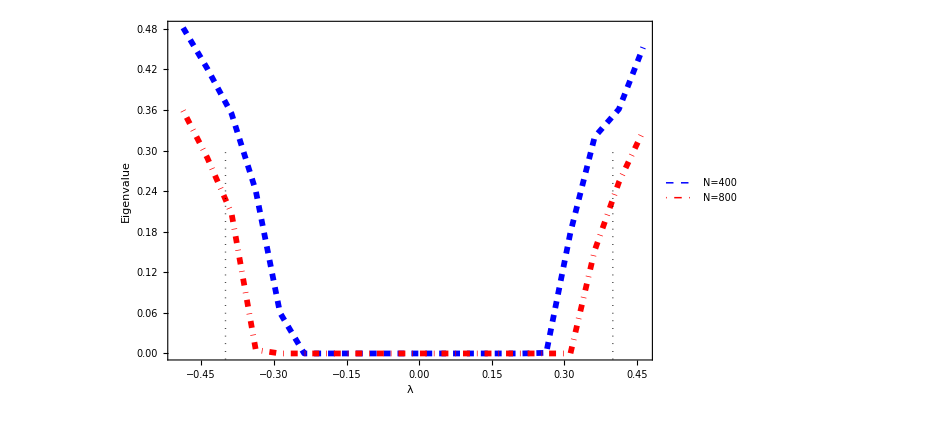

```mathematica
ListPlot[{Eigs4001,Eigs8001},PlotRange->All,Joined->True,PlotStyle->{{Thickness[0.006],Blue,Dashed},{Thickness[0.006],Red,DotDashed}}, Frame->True,FrameLabel->{"λ", "Eigenvalue"},LabelStyle->{22,Black},PlotLegends->Placed[LineLegend[{"N=400","N=800","N=1600","N=3200"},LabelStyle->{GrayLevel[0.5],Bold,30},LegendLayout->{"Row",2}],{0.5,0.5}],AxesOrigin->{-0.5,0},Epilog->{Thick,Black,Dotted,Line[Tab1],Line[Tab2]}]
```

```mathematica
(*with disorder*)
Ntval=400;h1val = 1.0; h2val = 1.0;h3val=1.0;h4val=1.0;Elval=0.05;Eaval=1.0;
s1val = 10.0;s2val =1.0;t1val = 1Exp[-1/4];t2val = 1.5Exp[1/4]; b1val = 1.5Exp[1/4];b2val = 1.0Exp[-1/4];
AbsoluteTiming[Eigs4001d=Table[{λ,Abs[Eigenvalues[Re[HRectangleF2[s1val, s2val, t1val,t2val, b1val, b2val, h1val, h2val,h3val,h4val,Eaval,Elval,Ntval,   λ]],-1,Method->{"Arnoldi",BasisSize->Ntval,MaxIterations->100000,"Criteria"->"Magnitude"}][[1]]]},
{λ,-0.4875,0.4875,0.05}];]
```

{467.66904,Null}

```mathematica
Ntval=600;h1val = 1.0; h2val = 1.0;h3val=1.0;h4val=1.0;Elval=0.05;Eaval=1.0;
s1val = 10.0;s2val =1.0;t1val = 1Exp[-1/4];t2val = 1.5Exp[1/4]; b1val = 1.5Exp[1/4];b2val = 1.0Exp[-1/4];
AbsoluteTiming[Eigs6001d=Table[{λ,Abs[Eigenvalues[Re[HRectangleF2[s1val, s2val, t1val,t2val, b1val, b2val, h1val, h2val,h3val,h4val,Eaval,Elval,Ntval,   λ]],-1,Method->{"Arnoldi",BasisSize->Ntval,MaxIterations->100000,"Criteria"->"Magnitude"}][[1]]]},
{λ,-0.4875,0.4875,0.05}];]
```

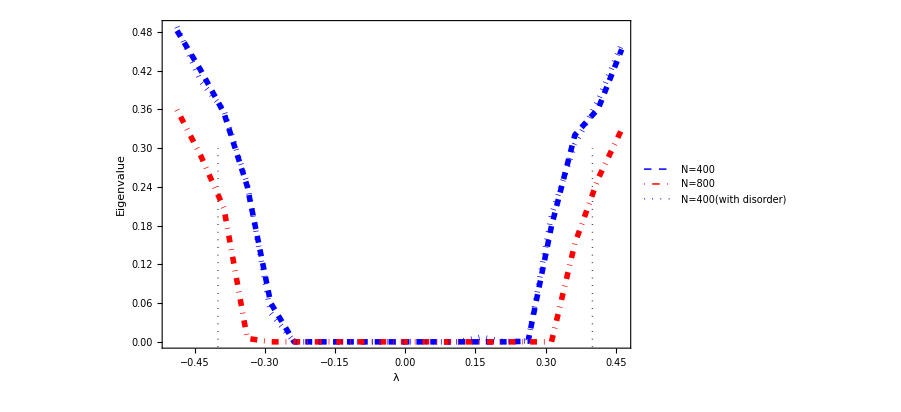

```mathematica
ListPlot[{Eigs4001,Eigs4001d,Eigs6001d,Eigs8001},PlotRange->All,Joined->True,PlotStyle->{{Thickness[0.006],Blue,Dashed},{Thickness[0.006],Red,DotDashed},{Thickness[0.006],Black,Dotted},{Thickness[0.006],Green,Dotted}}, Frame->True,FrameLabel->{"λ", "Eigenvalue"},LabelStyle->{22,Black},PlotLegends->Placed[LineLegend[{"N=400","N=400(with disorder)","N=600 (With disorder)","N=800"},LabelStyle->{GrayLevel[0.5],Bold,30},LegendLayout->{"Row",2}],{0.5,0.5}],AxesOrigin->{-0.5,0},Epilog->{Thick,Black,Dotted,Line[Tab1],Line[Tab2]}]
```

```mathematica
s1val = 2.0
λ1=-λup[4,1,2,1,s1val/(1+Exp[-EtIn1[20,Ntval,1,s2val,1.0]]),s1val/(1+Exp[EtIn1[20,Ntval,1,s2val,1.0]])]
λ2=-λdown[4,1,2,1,s1val/(1+Exp[-EtIn1[20,Ntval,1,s2val,1.0]]),s1val/(1+Exp[EtIn1[20,Ntval,1,s2val,1.0]])]
Tab1={{λ1,-0.02},{λ1,1.30}}
Tab2={{λ2,-0.02},{λ2,1.30}}
```

2.

-0.4365

0.815001

{{-0.4365,-0.02},{-0.4365,1.3}}

{{0.815001,-0.02},{0.815001,1.3}}

```mathematica
Ntval=800;h1val = 1.0; h2val = 1.0;h3val=1.0;h4val=1.0;Elval=0.1;Eaval=1.0;
s1val = 2.0;s2val =1.0;t1val = 1Exp[-1/4];t2val = 4.0Exp[1/4]; b1val = 2.0Exp[1/4];b2val = 1.0Exp[-1/4];

AbsoluteTiming[Eigs2800=Table[{λ,Abs[Eigenvalues[HRectangleF2[s1val, s2val, t1val,t2val, b1val, b2val, h1val, h2val,h3val,h4val,Eaval,Elval,Ntval,    λ],-1,Method->{"Arnoldi",BasisSize->120,MaxIterations->100000,Tolerance->Automatic}][[1]]]},
{λ,-0.95,0.95,0.025}];]
```

{2652.82799,Null}

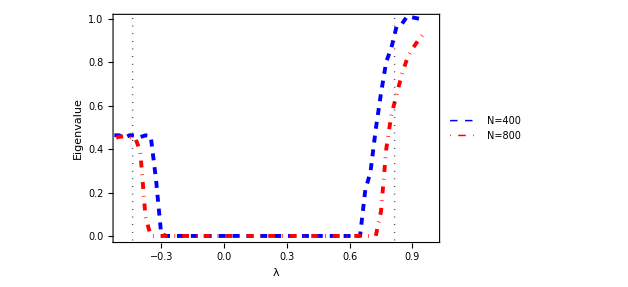

```mathematica
ListPlot[{Eigs2400,Eigs2800},PlotRange->{{-0.5,1.0},{-0.01,1}},Joined->True,PlotStyle->{{Thickness[0.006],Blue,Dashed},{Thickness[0.006],Red,DotDashed}}, Frame->True,FrameLabel->{"λ", "Eigenvalue"},LabelStyle->{22,Black},PlotLegends->Placed[LineLegend[{"N=400","N=800","N=1600","N=3200"},LabelStyle->{GrayLevel[0.5],Bold,30},LegendLayout->{"Row",2}],{0.5,0.5}],AxesOrigin->{-1,0},Epilog->{Thick,Black,Dotted,Line[Tab1],Line[Tab2]}]
```

```mathematica
s1val = 2.0
λ1=-λup[2,1,2,1,s1val/(1+Exp[-EtIn1[20,Ntval,1,s2val,1.0]]),s1val/(1+Exp[EtIn1[20,Ntval,1,s2val,1.0]])]
λ2=-λdown[2,1,2,1,s1val/(1+Exp[-EtIn1[20,Ntval,1,s2val,1.0]]),s1val/(1+Exp[EtIn1[20,Ntval,1,s2val,1.0]])]
Tab1={{λ1,-0.02},{λ1,1.30}}
Tab2={{λ2,-0.02},{λ2,1.30}}
```

2.

-0.661

0.661001

{{-0.661,-0.02},{-0.661,1.3}}

{{0.661001,-0.02},{0.661001,1.3}}

```mathematica
Ntval=100;h1val = 1.0; h2val = 1.0;h3val=1.0;h4val=1.0;Elval=0.1;Eaval=1.0;
s1val = 2.0;s2val =1.0;t1val = 1Exp[-1/4];t2val = 4.0Exp[1/4]; b1val = 1.1Exp[1/4];b2val = 1.0Exp[-1/4];

AbsoluteTiming[Eigs2100=Table[{λ,Abs[Eigenvalues[HRectangleF2[s1val, s2val, t1val,t2val, b1val, b2val, h1val, h2val,h3val,h4val,Eaval,Elval,Ntval,    λ],-1,Method->{"Arnoldi",BasisSize->120,MaxIterations->100000,Tolerance->Automatic}][[1]]]},
{λ,-0.95,0.95,0.025}];]
```

{26.73851,Null}

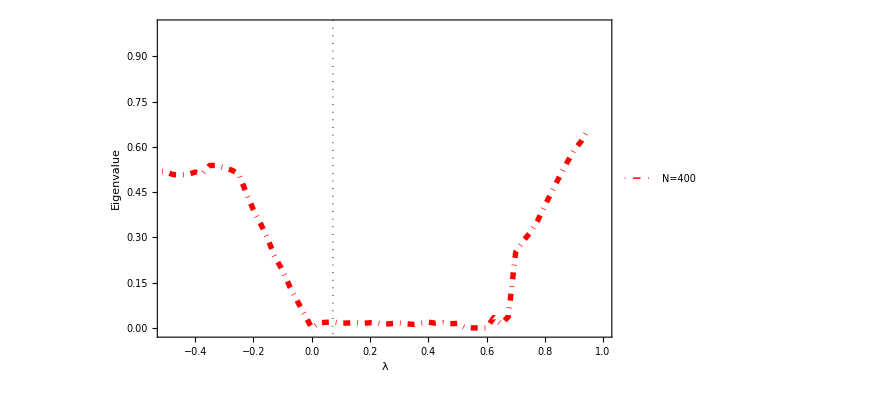

```mathematica
ListPlot[{Eigs2100},PlotRange->{{-0.5,1.0},{-0.01,1}},Joined->True,PlotStyle->{{Thickness[0.006],Blue,Dashed},{Thickness[0.006],Red,DotDashed}}, Frame->True,FrameLabel->{"λ", "Eigenvalue"},LabelStyle->{22,Black},PlotLegends->Placed[LineLegend[{"N=400","N=800","N=1600","N=3200"},LabelStyle->{GrayLevel[0.5],Bold,30},LegendLayout->{"Row",2}],{0.5,0.5}],AxesOrigin->{-1,0},Epilog->{Thick,Black,Dotted,Line[Tab1],Line[Tab2]}]
```

```mathematica
(*HRectangle in which the square root of W is taken. *)
Ntval=1000;h1val = 1.0; h2val = 1.0;h3val=1.0;h4val=1.0;Elval=0.1;Eaval=1.0;
s1val = 2.0;s2val =1.0;t1val = 1Exp[-1/4];t2val = 4.0Exp[1/4]; b1val = 2.0Exp[1/4];b2val = 1.0Exp[-1/4];

AbsoluteTiming[Eigs21000p=Table[{λ,Abs[Eigenvalues[HRectangleF2[s1val, s2val, t1val,t2val, b1val, b2val, h1val, h2val,h3val,h4val,Eaval,Elval,Ntval,   ⅈ λ],-1,Method->{"Arnoldi",BasisSize->120,MaxIterations->100000,Tolerance->Automatic}][[1]]]},
{λ,0.35,0.50,0.025}];]
```

{399.86181,Null}

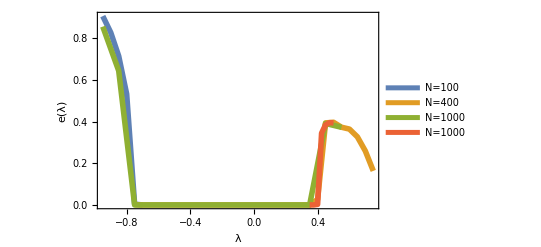

```mathematica
ListPlot[{Eigs2800p,Eigs2800,Eigs21000,Eigs21000p},PlotRange->All,Joined->True,PlotStyle->{Thickness[0.01]},PlotLegends->{"N=100","N=400","N=1000","N=1000"}, Frame->True,FrameLabel->{"λ", "e(λ)"},LabelStyle->22]
```

{17.55331,Null}

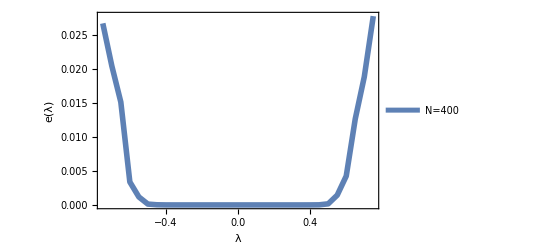

```mathematica
(*Disordered Interface size 20*)
Ntval=100;h1val = 1.0; h2val = 1.0;h3val=1.0;h4val=1.0;Elval=0.1;Eaval=1.0;
s1val = 2.0;s2val =1.0;t1val = 1Exp[-1/4];t2val = 2.0Exp[1/4]; b1val = 2.0Exp[1/4];b2val = 1.0Exp[-1/4];


AbsoluteTiming[Eigs2100=Table[{λ,Abs[Eigenvalues[HRectangleF[s1val, s2val, t1val,t2val, b1val, b2val, h1val, h2val,h3val,h4val,Eaval,Elval,Ntval,   λ],-1,Method->{"Arnoldi",BasisSize->120,MaxIterations->100000,Tolerance->Automatic}][[1]]]},
{λ,-0.75,0.75,0.05}];]
ListPlot[{Eigs2100},PlotRange->All,Joined->True,PlotStyle->{Thickness[0.01]},PlotLegends->{"N=400","N=800","N=1600","N=3200"}, Frame->True,FrameLabel->{"λ", "e(λ)"},LabelStyle->22]
```

{352.7767,Null}

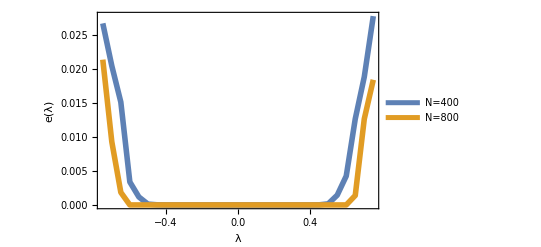

```mathematica
(*Disordered, Interface size 20*)
Ntval=400;h1val = 1.0; h2val = 1.0;h3val=1.0;h4val=1.0;Elval=0.1;Eaval=1.0;
s1val = 2.0;s2val =1.0;t1val = 1Exp[-1/4];t2val = 2.0Exp[1/4]; b1val = 2.0Exp[1/4];b2val = 1.0Exp[-1/4];


AbsoluteTiming[Eigs2400=Table[{λ,Abs[Eigenvalues[HRectangleF[s1val, s2val, t1val,t2val, b1val, b2val, h1val, h2val,h3val,h4val,Eaval,Elval,Ntval,   λ],-1,Method->{"Arnoldi",BasisSize->120,MaxIterations->100000,Tolerance->Automatic}][[1]]]},
{λ,-0.75,0.75,0.05}];]
ListPlot[{Eigs2100,Eigs2400},PlotRange->All,Joined->True,PlotStyle->{Thickness[0.01]},PlotLegends->{"N=400","N=800","N=1600","N=3200"}, Frame->True,FrameLabel->{"λ", "e(λ)"},LabelStyle->22]
```

{1072.62189,Null}

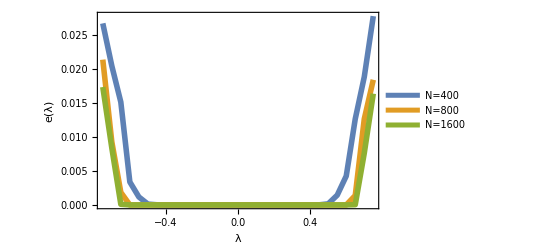

```mathematica
Ntval=800;h1val = 1.0; h2val = 1.0;h3val=1.0;h4val=1.0;Elval=0.1;Eaval=1.0;
s1val = 2.0;s2val =1.0;t1val = 1Exp[-1/4];t2val = 2.0Exp[1/4]; b1val = 2.0Exp[1/4];b2val = 1.0Exp[-1/4];


AbsoluteTiming[Eigs2800=Table[{λ,Abs[Eigenvalues[HRectangleF[s1val, s2val, t1val,t2val, b1val, b2val, h1val, h2val,h3val,h4val,Eaval,Elval,Ntval,   λ],-1,Method->{"Arnoldi",BasisSize->120,MaxIterations->100000,Tolerance->Automatic}][[1]]]},
{λ,-0.75,0.75,0.05}];]
ListPlot[{Eigs2100,Eigs2400,Eigs2800},PlotRange->All,Joined->True,PlotStyle->{Thickness[0.01]},PlotLegends->{"N=400","N=800","N=1600","N=3200"}, Frame->True,FrameLabel->{"λ", "e(λ)"},LabelStyle->22]
```

```mathematica
λ1=λup[2,1,2,1,s1val/(1+Exp[-EtIn1[20,Ntval,1,s2val,1.0]]),s1val/(1+Exp[EtIn1[20,Ntval,1,s2val,1.0]])]
λ2=λdown[2,1,2,1,s1val/(1+Exp[-EtIn1[20,Ntval,1,s2val,1.0]]),s1val/(1+Exp[EtIn1[20,Ntval,1,s2val,1.0]])]
Tab1={{λ1,-0.02},{λ1,0.50}}
Tab2={{λ2,-0.02},{λ2,0.50}}
```

0.661

-0.661001

{{0.661,-0.02},{0.661,0.5}}

{{-0.661001,-0.02},{-0.661001,0.5}}

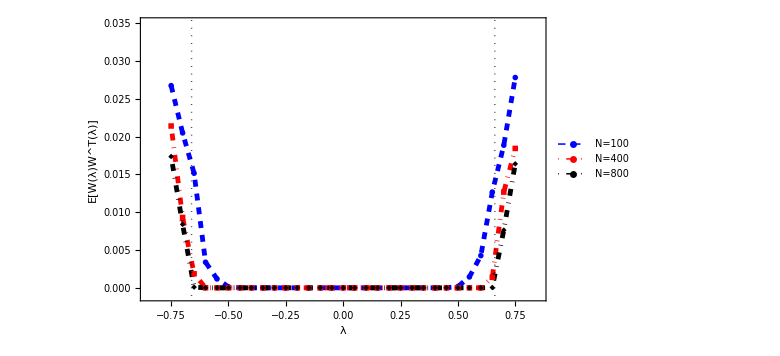

```mathematica
ListPlot[{Eigs2100,Eigs2400,Eigs2800},PlotRange->{{-0.85,0.85},{-0.001,0.035}},PlotMarkers->{Automatic,Large},Joined->True,PlotStyle->{{Thickness[0.006],Blue,Dashed},{Thickness[0.006],Red,DotDashed},{Thickness[0.006],Black,DotDashed}}, Frame->True,FrameLabel->{"λ", "E[W(λ)W^T(λ)]"},LabelStyle->{30,Black},PlotLegends->Placed[LineLegend[{"N=100","N=400","N=800","N=3200"},LabelStyle->{GrayLevel[0.5],Bold,30},LegendLayout->{"Row",3}],{0.5,0.5}],AxesOrigin->{-1,0},Epilog->{Thick,Black,Dotted,Line[Tab1],Line[Tab2]}]
```

```mathematica
s1val = 2.0
λ1=-λup[4,1,2,1,s1val/(1+Exp[-EtIn1[20,Ntval,1,s2val,1.0]]),s1val/(1+Exp[EtIn1[20,Ntval,1,s2val,1.0]])]
λ2=-λdown[4,1,2,1,s1val/(1+Exp[-EtIn1[20,Ntval,1,s2val,1.0]]),s1val/(1+Exp[EtIn1[20,Ntval,1,s2val,1.0]])]
Tab1={{λ1,-0.02},{λ1,1.30}}
Tab2={{λ2,-0.02},{λ2,1.30}}

λ1=λup[4,1,4,1,s1val/(1+Exp[-EtIn1[20,Ntval,1,s2val,1.0]]),s1val/(1+Exp[EtIn1[20,Ntval,1,s2val,1.0]])]
λ2=λdown[4,1,4,1,s1val/(1+Exp[-EtIn1[20,Ntval,1,s2val,1.0]]),s1val/(1+Exp[EtIn1[20,Ntval,1,s2val,1.0]])]
Tab1={{λ1,-0.02},{λ1,0.50}}
Tab2={{λ2,-0.02},{λ2,0.50}}

λ1=λup[2,1,2,1,s1val/(1+Exp[-EtIn1[20,Ntval,1,s2val,1.0]]),s1val/(1+Exp[EtIn1[20,Ntval,1,s2val,1.0]])]
λ2=λdown[2,1,2,1,s1val/(1+Exp[-EtIn1[20,Ntval,1,s2val,1.0]]),s1val/(1+Exp[EtIn1[20,Ntval,1,s2val,1.0]])]
Tab1={{λ1,-0.02},{λ1,0.50}}
Tab2={{λ2,-0.02},{λ2,0.50}}
```

2.

-0.4365

0.815001

{{-0.4365,-0.02},{-0.4365,1.3}}

{{0.815001,-0.02},{0.815001,1.3}}

0.4585

-0.458501

{{0.4585,-0.02},{0.4585,0.5}}

{{-0.458501,-0.02},{-0.458501,0.5}}

0.661

-0.661001

{{0.661,-0.02},{0.661,0.5}}

{{-0.661001,-0.02},{-0.661001,0.5}}

{11.4469,Null}

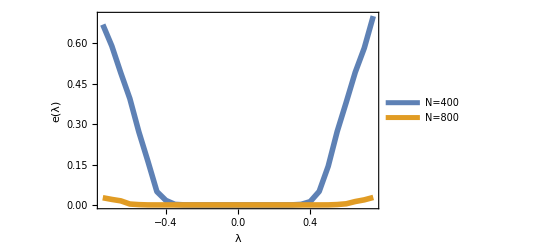

```mathematica
(*Disordered Interface size 20*)
Ntval=100;h1val = 1.0; h2val = 1.0;h3val=1.0;h4val=1.0;Elval=0.1;Eaval=1.0;
s1val = 2.0;s2val =1.0;t1val = 1Exp[-1/4];t2val = 4.0Exp[1/4]; b1val = 4.0Exp[1/4];b2val = 1.0Exp[-1/4];


AbsoluteTiming[Eigs21004=Table[{λ,Abs[Eigenvalues[HRectangleF[s1val, s2val, t1val,t2val, b1val, b2val, h1val, h2val,h3val,h4val,Eaval,Elval,Ntval,   λ],-1,Method->{"Arnoldi",BasisSize->120,MaxIterations->100000,Tolerance->Automatic}][[1]]]},
{λ,-0.75,0.75,0.05}];]
ListPlot[{Eigs21004,Eigs2100},PlotRange->All,Joined->True,PlotStyle->{Thickness[0.01]},PlotLegends->{"N=400","N=800","N=1600","N=3200"}, Frame->True,FrameLabel->{"λ", "e(λ)"},LabelStyle->22]
```

```mathematica
Ntval=400;h1val = 1.0; h2val = 1.0;h3val=1.0;h4val=1.0;Elval=0.1;Eaval=1.0;
s1val = 2.0;s2val =1.0;t1val = 1Exp[-1/4];t2val = 4.0Exp[1/4]; b1val = 4.0Exp[1/4];b2val = 1.0Exp[-1/4];


AbsoluteTiming[Eigs24004=Table[{λ,Abs[Eigenvalues[HRectangleF[s1val, s2val, t1val,t2val, b1val, b2val, h1val, h2val,h3val,h4val,Eaval,Elval,Ntval,   λ],-1,Method->{"Arnoldi",BasisSize->120,MaxIterations->100000,Tolerance->Automatic}][[1]]]},
{λ,-0.75,0.75,0.05}];]
```

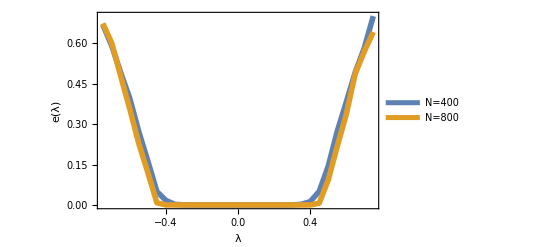

```mathematica
ListPlot[{Eigs21004,Eigs24004},PlotRange->All,Joined->True,PlotStyle->{Thickness[0.01]},PlotLegends->{"N=400","N=800","N=1600","N=3200"}, Frame->True,FrameLabel->{"λ", "e(λ)"},LabelStyle->22]
```

```mathematica
Ntval=800;h1val = 1.0; h2val = 1.0;h3val=1.0;h4val=1.0;Elval=0.1;Eaval=1.0;
s1val = 2.0;s2val =1.0;t1val = 1Exp[-1/4];t2val = 4.0Exp[1/4]; b1val = 4.0Exp[1/4];b2val = 1.0Exp[-1/4];


AbsoluteTiming[Eigs28004=Table[{λ,Abs[Eigenvalues[HRectangleF[s1val, s2val, t1val,t2val, b1val, b2val, h1val, h2val,h3val,h4val,Eaval,Elval,Ntval,   λ],-1,Method->{"Arnoldi",BasisSize->120,MaxIterations->100000,Tolerance->Automatic}][[1]]]},
{λ,-0.75,0.75,0.05}];]
```

{1028.01007,Null}

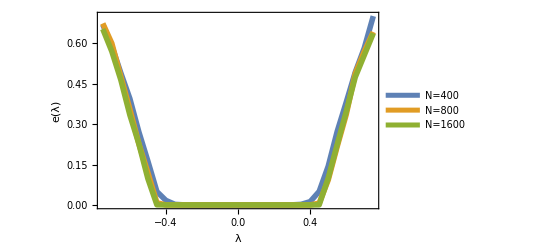

```mathematica
ListPlot[{Eigs21004,Eigs24004,Eigs28004},PlotRange->All,Joined->True,PlotStyle->{Thickness[0.01]},PlotLegends->{"N=400","N=800","N=1600","N=3200"}, Frame->True,FrameLabel->{"λ", "e(λ)"},LabelStyle->22]
```

```mathematica
Eig400[[1,1]]
```

-0.5

```mathematica
StringTake[Eig400[[17,2]],{2,9}]
```

0.029472

```mathematica
StringTake[Eig400[[17,3]],{1,22}]
```

```mathematica
"1.3909857744586263*^-7"
```

```mathematica
"1.3909857744586263*10^-7"
```

1.3909857744586263*10^-7

```mathematica
Ntval=400;h1val = 1.0; h2val = 1.0;h3val=1.0;h4val=1.0;Elval=0.0;Eaval=1.0;
s1val = 10.0;s2val =1.0;t1val = 1.Exp[-1./4.];t2val = 1.5Exp[1./4.]; b1val = 1.5Exp[1./4.];b2val = 1.0Exp[-1./4.];
Wopt=WRectangleAllLinksSqJControl[s1val, s2val, t1val,t2val, b1val, b2val, h1val, h2val,h3val,h4val,Eaval,Elval,Ntval];
mwopt=Min[Wopt];
Woptvec=Re[WRectangleAllLinksSqJOptimized[s1val, s2val, t1val,t2val, b1val, b2val, h1val, h2val,h3val,h4val,Eaval,Elval,Ntval,    0.0,Wopt]];
startvec=Re[Eigenvectors[Woptvec,1,Method->{"Arnoldi",BasisSize->2*Ntval,MaxIterations->500000,"Criteria"->"RealPart"}][[1]]];
AbsoluteTiming[Chop[Eigenvalues[Re[WRectangleAllLinksSqJOptimized[s1val, s2val, t1val,t2val, b1val, b2val, h1val, h2val,h3val,h4val,Eaval,Elval,Ntval,    0.275,Wopt]-IdentityMatrix[2*Ntval]*mwopt],2,Method->{"Arnoldi",BasisSize->Ntval,MaxIterations->10000000,"Criteria"->"RealPart"}]]+mwopt]
AbsoluteTiming[Chop[Eigenvalues[WRectangleAllLinksSqJOptimized[s1val, s2val, t1val,t2val, b1val, b2val, h1val, h2val,h3val,h4val,Eaval,Elval,Ntval,    0.275,Wopt],2,Method->{"Arnoldi",BasisSize->2*Ntval,MaxIterations->10000000,"Criteria"->"RealPart"}]]]
AbsoluteTiming[Chop[Eigenvalues[WRectangleAllLinksSqJOptimized[s1val, s2val, t1val,t2val, b1val, b2val, h1val, h2val,h3val,h4val,Eaval,Elval,Ntval,    0.275,Wopt],2,Method->{"Arnoldi",BasisSize->Ntval,MaxIterations->10000000,"Criteria"->"RealPart"}]]]
AbsoluteTiming[Chop[Eigenvalues[WRectangleAllLinksSqJOptimized[s1val, s2val, t1val,t2val, b1val, b2val, h1val, h2val,h3val,h4val,Eaval,Elval,Ntval,    0.275,Wopt],-1,Method->{"Arnoldi",BasisSize->Ntval,MaxIterations->10000000,"Criteria"->"Magnitude"}]]]
```

{2.80661,{0.101614,0.100638+0.0560337 ⅈ}}

{7.10001,{0.0698816+0.0115878 ⅈ,0.0698816-0.0115878 ⅈ}}

{2.5035,{0.100638+0.0560339 ⅈ,0.100638-0.0560339 ⅈ}}

{1.36494,{0}}

```mathematica
Ntval=600;h1val = 1.0; h2val = 1.0;h3val=1.0;h4val=1.0;Elval=0.0;Eaval=1.0;
s1val = 10.0;s2val =1.0;t1val = 1.Exp[-1./4.];t2val = 1.5Exp[1./4.]; b1val = 1.5Exp[1./4.];b2val = 1.0Exp[-1./4.];
Wopt=WRectangleAllLinksSqJControl[s1val, s2val, t1val,t2val, b1val, b2val, h1val, h2val,h3val,h4val,Eaval,Elval,Ntval];
mwopt=Min[Wopt];
Woptvec=Re[WRectangleAllLinksSqJOptimized[s1val, s2val, t1val,t2val, b1val, b2val, h1val, h2val,h3val,h4val,Eaval,Elval,Ntval,    0.0,Wopt]];
startvec=Re[Eigenvectors[Woptvec,1,Method->{"Arnoldi",BasisSize->2*Ntval,MaxIterations->500000,"Criteria"->"RealPart"}][[1]]];
AbsoluteTiming[Chop[Eigenvalues[Re[WRectangleAllLinksSqJOptimized[s1val, s2val, t1val,t2val, b1val, b2val, h1val, h2val,h3val,h4val,Eaval,Elval,Ntval,    0.275,Wopt]-IdentityMatrix[2*Ntval]*mwopt],2,Method->{"Arnoldi",BasisSize->Ntval,MaxIterations->10000000,"Criteria"->"RealPart",Tolerance->10^(-7)}]]+mwopt]
AbsoluteTiming[Chop[Eigenvalues[WRectangleAllLinksSqJOptimized[s1val, s2val, t1val,t2val, b1val, b2val, h1val, h2val,h3val,h4val,Eaval,Elval,Ntval,    0.275,Wopt],1,Method->{"Arnoldi",BasisSize->Ntval,MaxIterations->10000000,"Criteria"->"RealPart"}]]]
AbsoluteTiming[Chop[Eigenvalues[WRectangleAllLinksSqJOptimized[s1val, s2val, t1val,t2val, b1val, b2val, h1val, h2val,h3val,h4val,Eaval,Elval,Ntval,    0.275,Wopt],-1,Method->{"Arnoldi",BasisSize->Ntval,MaxIterations->10000000,"Criteria"->"Magnitude"}]]]
testvec1=Eigenvectors[WRectangleAllLinksSqJOptimized[s1val, s2val, t1val,t2val, b1val, b2val, h1val, h2val,h3val,h4val,Eaval,Elval,Ntval,    0.275,Wopt],-1,Method->{"Arnoldi",BasisSize->Ntval,MaxIterations->10000000,"Criteria"->"Magnitude"}][[1]];
testvec2=Eigenvectors[WRectangleAllLinksSqJOptimized[s1val, s2val, t1val,t2val, b1val, b2val, h1val, h2val,h3val,h4val,Eaval,Elval,Ntval,    0.275,Wopt],1,Method->{"Arnoldi",BasisSize->Ntval,MaxIterations->10000000,"Criteria"->"RealPart"}][[1]];
```

{2.90118,{0.101614}}

{2.52179,{0.101614}}

{1.34641,{0}}

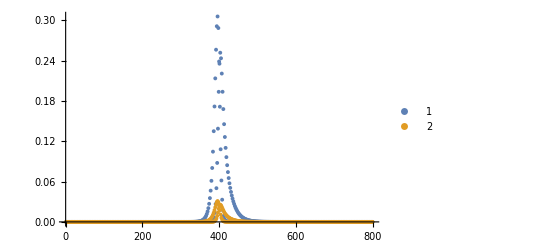

```mathematica
ListPlot[{testvec2,WRectangleAllLinksSqJOptimized[s1val, s2val, t1val,t2val, b1val, b2val, h1val, h2val,h3val,h4val,Eaval,Elval,Ntval,    0.275,Wopt].testvec2},PlotLegends->Automatic,PlotRange->All]
```

10.

-1.107

1.107

0.05

{0.25309}

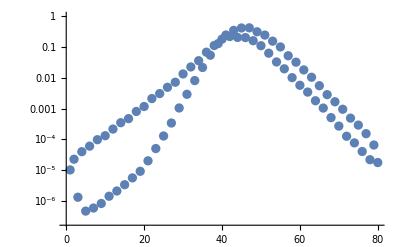

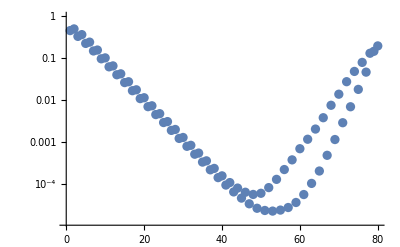

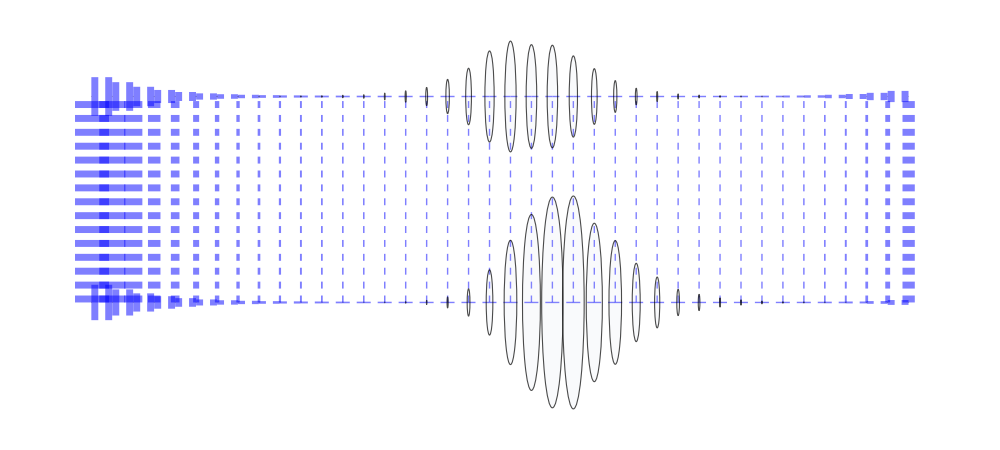

```mathematica
s1val = 10.0
λ1=-λup[5,1,5,1,s1val/(1+Exp[-EtIn1[20,Ntval,1,s2val,1.0]]),s1val/(1+Exp[EtIn1[20,Ntval,1,s2val,1.0]])]
λ2=-λdown[5,1,5,1,s1val/(1+Exp[-EtIn1[20,Ntval,1,s2val,1.0]]),s1val/(1+Exp[EtIn1[20,Ntval,1,s2val,1.0]])]

Ntval=40;h1val = 1.0; h2val = 1.0;h3val=1.0;h4val=1.0;Elval=0.1;Eaval=1.0;
s1val = 10;s2val =1.0;t1val = 1Exp[-1/4];t2val = 5Exp[1/4]; b1val = 5Exp[1/4];b2val = 1.0Exp[-1/4];λval=-0.5;ϵval=0.05
trans=GridGraph[{2,Ntval},GraphLayout->{"GridEmbedding","Dimension"->{2,Ntval}}];
t=EdgeList[trans];
l=VertexList[Graph[trans]];


WF1=WRectangleAllLinksSqJ[s1val, s2val, t1val,t2val, b1val, b2val, h1val, h2val,h3val,h4val,Eaval,Elval,Ntval,    λval];
Eigenvalues[WF1,-1,Method->{"Arnoldi",BasisSize->Ntval,MaxIterations->10000000,"Criteria"->"Magnitude"}]


(*u1=Eigenvectors[WT1,-1][[1]];
u0=Eigenvectors[W0,-1][[1]];
v1=Eigenvectors[Transpose[WT1],-1][[1]];
v0=Eigenvectors[Transpose[W0],-1][[1]];
*)
u0=Eigenvectors[Transpose[WF1],-1][[1]];(*uo==Transpose*)
u1=Eigenvectors[WF1,-1][[1]];
v1=Eigenvectors[WF1,-1][[1]];
v0=Eigenvectors[Transpose[WF1],-1][[1]];
ListLogPlot[Abs[u1]]
ListLogPlot[Abs[u0]]

e00=u0;(*e00 gets mapped onto the edges, as it should be*)
e11=u1;(*e11 gets mapped onto vertices as it shoudl be*)
e00=10e00/(Mean[e00]);
e11=10e11/(Mean[e11]*2*Ntval);
vs=Transpose@{l,Abs[e11]+0.0}/.List[a_,b_]->Rule[a,b];

es=(First@#->Directive[Thickness[Last@#],Opacity[.5]])&/@Transpose@{t,EdgeSteadyState[e00,t]};
(*Weigths for vertices*)
g=Graph[trans,VertexShapeFunction->"Circle",VertexSize->vs,VertexStyle->{Opacity[0.06]},EdgeStyle->es,EdgeShapeFunction->({Blue,Dashed,Line[#1]}&),ImageSize->1000,AspectRatio->0.45]
g1=HighlightGraph[g,{#,Style[#,{Opacity[0.6],Hue@{.1 }}]}&/@VertexList[g]]
Export["/Users/rusi/Google Drive/topological-phases_1/Localized1a.eps",g1,ImageSize->100000,Frame->True]
```

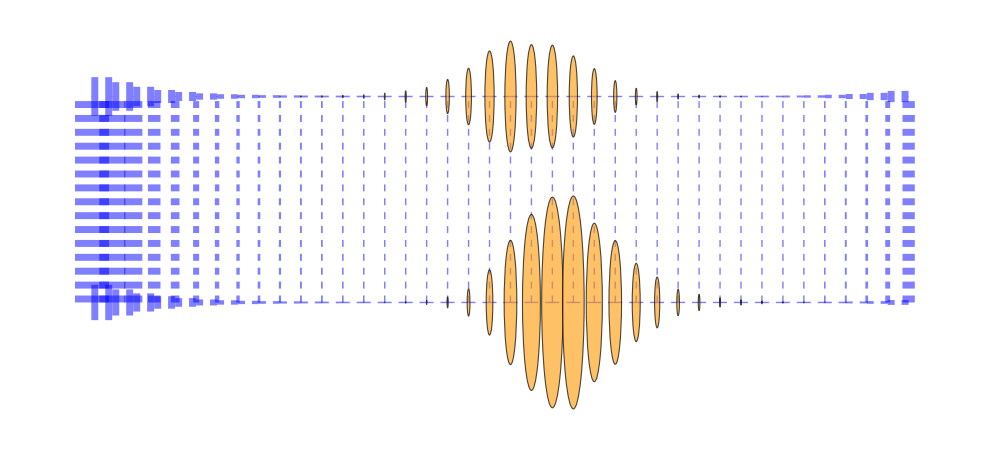

/Users/rusi/Google Drive/topological-phases_1/Localized1a.eps

Set::write: Tag Inherited in Inherited["State"] is Protected.

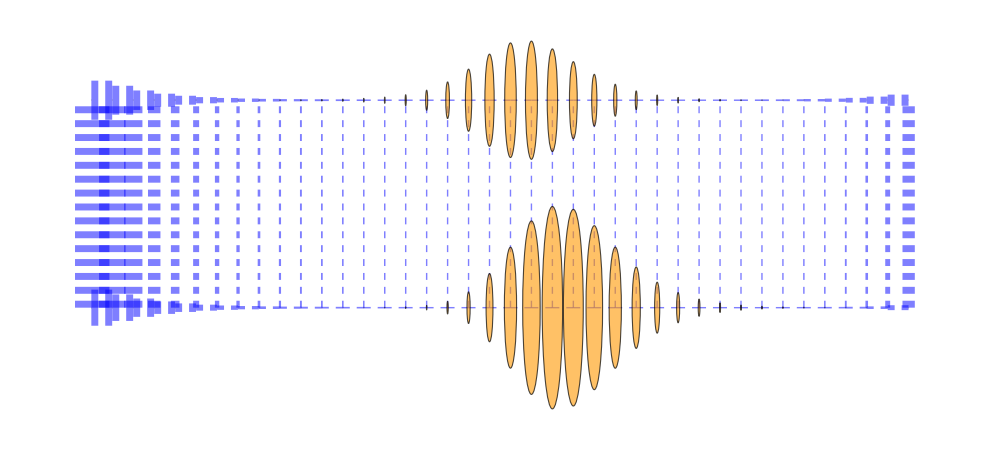

/Users/rusi/Google Drive/topological-phases_1/Localized1a.eps

Set::write: Tag Inherited in Inherited["State"] is Protected.

```mathematica
vs
```

{1→0.000020139,2→0.0000495404,3→2.58062×10^-6,4→0.000080961,5→1.02729×10^-6,6→0.000126332,7→1.28761×10^-6,8→0.000196539,9→1.97098×10^-6,10→0.000305703,11→3.06481×10^-6,12→0.000475504,13→4.77939×10^-6,14→0.000739673,15→7.49879×10^-6,16→0.00115086,17→0.000011995,18→0.00179183,19→0.0000203494,20→0.00279513,21→0.0000403182,22→0.00438002,23→0.000106724,24→0.00690091,25→0.000293265,26→0.010993,27→0.000832144,28→0.0178772,29→0.00243879,30→0.0300941,31→0.00729149,32→0.053025,33→0.0215918,34→0.0969707,35→0.0605602,36→0.17655,37→0.152665,38→0.29957,39→0.328907,40→0.444207,41→0.583083,42→0.552367,43→0.836215,44→0.569789,45→0.975785,46→0.494624,47→0.947921,48→0.371728,49→0.790536,50→0.249708,51→0.583876,52→0.154372,53→0.392578,54→0.0899501,55→0.245804,56→0.0503112,57→0.145917,58→0.0273745,59→0.0832712,60→0.0146288,61→0.0461519,62→0.00780346,63→0.0251572,64→0.00416491,65→0.0135898,66→0.00222361,67→0.00730424,68→0.00118738,69→0.00391416,70→0.000634102,71→0.0020928,72→0.000338643,73→0.0011155,74→0.000180843,75→0.00058993,76→0.0000965638,77→0.000304215,78→0.0000519176,79→0.000141941,80→0.000038406}

```mathematica
e11
```

{0.000020139+0. ⅈ,0.0000495404+0. ⅈ,2.58062×10^-6+0. ⅈ,0.000080961+0. ⅈ,1.02729×10^-6+0. ⅈ,0.000126332+0. ⅈ,1.28761×10^-6+0. ⅈ,0.000196539+0. ⅈ,1.97098×10^-6+0. ⅈ,0.000305703+0. ⅈ,3.06481×10^-6+0. ⅈ,0.000475504+0. ⅈ,4.77939×10^-6+0. ⅈ,0.000739673+0. ⅈ,7.49879×10^-6+0. ⅈ,0.00115086+0. ⅈ,0.000011995+0. ⅈ,0.00179183+0. ⅈ,0.0000203494+0. ⅈ,0.00279513+0. ⅈ,0.0000403182+0. ⅈ,0.00438002+0. ⅈ,0.000106724+0. ⅈ,0.00690091+0. ⅈ,0.000293265+0. ⅈ,0.010993+0. ⅈ,0.000832144+0. ⅈ,0.0178772+0. ⅈ,0.00243879+0. ⅈ,0.0300941+0. ⅈ,0.00729149+0. ⅈ,0.053025+0. ⅈ,0.0215918+0. ⅈ,0.0969707+0. ⅈ,0.0605602+0. ⅈ,0.17655+0. ⅈ,0.152665+0. ⅈ,0.29957+0. ⅈ,0.328907+0. ⅈ,0.444207+0. ⅈ,0.583083+0. ⅈ,0.552367+0. ⅈ,0.836215+0. ⅈ,0.569789+0. ⅈ,0.975785+0. ⅈ,0.494624+0. ⅈ,0.947921+0. ⅈ,0.371728+0. ⅈ,0.790536+0. ⅈ,0.249708+0. ⅈ,0.583876+0. ⅈ,0.154372+0. ⅈ,0.392578+0. ⅈ,0.0899501+0. ⅈ,0.245804+0. ⅈ,0.0503112+0. ⅈ,0.145917+0. ⅈ,0.0273745+0. ⅈ,0.0832712+0. ⅈ,0.0146288+0. ⅈ,0.0461519+0. ⅈ,0.00780346+0. ⅈ,0.0251572+0. ⅈ,0.00416491+0. ⅈ,0.0135898+0. ⅈ,0.00222361+0. ⅈ,0.00730424+0. ⅈ,0.00118738+0. ⅈ,0.00391416+0. ⅈ,0.000634102+0. ⅈ,0.0020928+0. ⅈ,0.000338643+0. ⅈ,0.0011155+0. ⅈ,0.000180843+0. ⅈ,0.00058993+0. ⅈ,0.0000965638+0. ⅈ,0.000304215+0. ⅈ,0.0000519176+0. ⅈ,0.000141941+0. ⅈ,0.000038406+0. ⅈ}

```mathematica
DSolve[y'[x]==x+c,x]
```

DSolve::argm: DSolve called with 2 arguments; 3 or more arguments are expected.

```mathematica
DSolve[y'[x]==c+y[x],y[x],x]
```

{{y[x]→-c+ⅇ^x C[1]}}

```mathematica
SeedRandom[10]
tempRandom=RandomInteger[1000]
```

683